Your Title Here

```mathematica
w1=7;w2=11;h1=7;h2=12;
```

```mathematica
r1=0.7;r2=0.9;
```

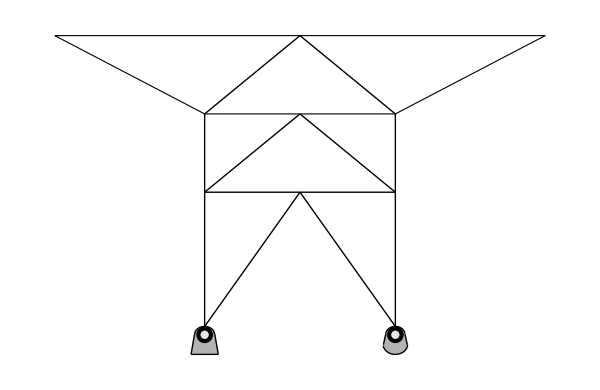

```mathematica
truss=Graphics[{Thick,
(*DRAWING TRUSS*)
(*{CapForm@"Round",Thickness@#1,#2,
{EdgeForm@{Thickness@#1,#2},FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}]}&@@@{{0.03,Black},{0.02,GrayLevel@0.6}},*)
{EdgeForm@Thick,FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}],

{GrayLevel@0.7,
Disk[{-w1,-0.75},0.75],Polygon[{{-w1-0.75,-0.75/2},{-w1+0.75,-0.75/2},{-w1+1,-2.5},{-w1-1,-2.5}}],
Disk[{w1,-r1},r1],Disk[{w1,-r1-r2},r2],Polygon[{{w1-r1,-0.65},{w1-0.875,-1.4},{w1+0.875,-1.4},{w1+r1,-0.65}}],
Black,
Line[{{-w1+#*0.75,-0.75},{-w1+#,-2.5}}]&/@{-1,1},Line[{{-w1-1,-2.5},{-w1+1,-2.5}}],Line[{#,√(0.75^2-(#+w1)^2)-0.75}&/@Range[-w1-0.75,-w1+0.75,0.1]],
Line[{#,√(r1^2-(#-w1)^2)-r1}&/@Range[w1-0.997*r1,w1+0.997*r1,0.001]],
Line[{#,-√(r2^2-(#-w1)^2)-r1-r2}&/@Range[w1-0.99*r2,w1+r2,0.01]],
Line[{{w1+#*r1,-0.65},{w1+#*0.875,-1.64}}]&/@{-1,1}},
{PointSize@0.02,Point@{#*w1,-0.75},GrayLevel@0.9,PointSize@0.01,Point@{#*w1,-0.75}}&/@{-1,1}
(*{PointSize@0.02,Point@#,GrayLevel@0.9,PointSize@0.01,Point@#}&/@{{-w1,-0.75},{w1,-0.75},{-w1,h2},{w1,h2},{-w1,h1+h2},{w1,h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2},{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2}}*)
},ImageSize->{600,390}]
```

```mathematica
labels=Graphics@{
Text[Framed[Style[Row@{" ",#1," "},18],RoundingRadius->15],#2,#3]&@@@{{"A",{-w1,0},{1.5,0}},{"B",{w1,0},{-1.5,0}},{"C",{w1,h2},{-1.5,0}},{"D",{w1,h1+h2},{-1.5,1}},{"E",{w1+w2,2*h1+h2},{-1.5,-1.5}},{"F",{0,2*h1+h2},{0,-1.5}},{"G",{-w1-w2,2*h1+h2},{1.5,-1.5}},{"H",{-w1,h1+h2},{1.5,1}},{"I",{-w1,h2},{1.5,0}},{"J",{0,h1+h2},{0,-1.5}},{"K",{0,h2},{0,-1.5}}}};
```

```mathematica
Manipulate[
Module[{θ1,θ2,θ3,sol,RAx,RAy,RB,F1,F2,F3,F4,F5,F6,F7,F8,F9,F10,F11,F12,F13,F14,F15,F16,F17,F18,scale,colC,colT},
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];

sol=Quiet@Solve[N@{
(*reactions*)rax+FEx==0,2*w1*rb+w2*(-FG)+(2*w1+w2)*(-FEy)+(2*h1+h2)*FEx==0,ray+rb-FG-FEy==0,
(*A*)f10*Cos[θ1]+RAx==0,f1+f10*Sin[θ1]+RAy==0,
(*B*)-f9*Cos[θ1]==0,f8+f9*Sin[θ1]+RB==0,
(*D*)-f15*Cos[θ3]-f16+f6*Cos[θ2]==0,-f7+f6*Sin[θ2]+f15*Sin[θ3]==0,
(*E*)-f6*Sin[θ2]-FEy==0,-f5-f6*Cos[θ2]+FEx==0,
(*F*)-f14*Sin[θ3]-f15*Sin[θ3]==0,-f4-f14*Cos[θ3]+f15*Cos[θ3]+f5==0,
(*G*)-FG-f3*Sin[θ2]==0,f3*Cos[θ2]+f4==0,
(*H*)-f3*Cos[θ2]+f13+f14*Cos[θ3]==0,f3*Sin[θ2]+f14*Sin[θ3]-f2==0,
(*I*)f11+f12*Cos[θ3]==0,
(*J*)-f12*Cos[θ3]-f13+f16+f17*Cos[θ3]==0,-f12*Sin[θ3]-f17*Sin[θ3]==0,
(*K*)-f10*Cos[θ1]-f11+f9*Cos[θ1]+f18==0
},{rax,ray,rb,f1,f2,f3,f4,f5,f6,f7,f8,f9,f10,f11,f12,f13,f14,f15,f16,f17,f18}][[1]];

RAx=rax/.sol;RAy=ray/.sol;RB=rb/.sol;
F1=f1/.sol;F2=f2/.sol;F3=f3/.sol;F4=f4/.sol;F5=f5/.sol;F6=f6/.sol;F7=f7/.sol;F8=f8/.sol;F9=f9/.sol;
F10=f10/.sol;F11=f11/.sol;F12=f12/.sol;F13=f13/.sol;F14=f14/.sol;F15=f15/.sol;F16=f16/.sol;
F17=f17/.sol;F18=f18/.sol;

scale[F_]:=2+5*Rescale[Abs@F,{0,4957}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Show[truss,(*If[showjoints,labels,{}],*)PlotRange->{{-22,28},{-9.5,31}},Epilog->{
{Thickness@0.01,Arrowheads@0.05,
Arrow[{{-(w1+w2),2*h1+h2},{-(w1+w2),h1+h2-scale[FG]}}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2,h1+h2-scale[FEy]}}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2+scale[FEx],2*h1+h2}}],
Arrow[{{-w1,If[RAy<1,1,-1]*scale[RAy]},{-w1,-0.11*h1}}],Arrow[{{-w1+scale[RAx],-0.1*h1},{-w1,-0.1*h1}}],
Arrow[{{w1,-scale[RB]},{w1,-0.1*h1}}]},
Text[Style[Row@{NumberForm[#1,{5,0}],Subscript[" lb","F"]},18],#2,#3]&@@@{{FG,{-w1-w2,h1+h2-scale[FG]},{0,1.5}},{FEy,{w1+w2,h1+h2-scale[FEy]},{0,1.5}},{FEx,{w1+w2+scale[FEx],2*h1+h2},{-1.2,0}},{RAx,{-w1+scale[RAx],-0.75},{-1.2,0}},{RAy,{-w1,-scale[If[RAy<0,700,RAy]]},{0,1.5}},{RB,{w1,-scale[RB]},{0,1.5}}},
(************************)


Flatten@{Thickness@0.005,Which[#1<0,{Arrowheads@{-0.035,0.035},colC},#1>0,{Arrowheads@{{0.035,0.315},{-0.035,0.675}},colT},#1==0,Black],If[#1==0,Line,Arrow]@#2}&@@@{
{F1,{{-w1,0},{-w1,h2}}},{F2,{{-w1,h2},{-w1,h1+h2}}},{F3,{{-w1,h1+h2},{-w1-w2,2*h1+h2}}},{F4,{{-w1-w2,2*h1+h2},{0,2*h1+h2}}},{F5,{{0,2*h1+h2},{w1+w2,2*h1+h2}}},{F6,{{w1,h1+h2},{w1+w2,2*h1+h2}}},{F7,{{w1,h2},{w1,h1+h2}}},{F8,{{w1,0},{w1,h2}}},{F9,{{w1,0},{0,h2}}},{F10,{{-w1,0},{0,h2}}},{F11,{{-w1,h2},{0,h2}}},{F12,{{-w1,h2},{0,h1+h2}}},{F13,{{-w1,h1+h2},{0,h1+h2}}},{F14,{{-w1,h1+h2},{0,2*h1+h2}}},{F15,{{w1,h1+h2},{0,2*h1+h2}}},{F16,{{0,h1+h2},{w1,h1+h2}}},{F17,{{w1,h2},{0,h1+h2}}},{F18,{{w1,h2},{0,h2}}}},

Text[Rotate[Style[Row@{" ",NumberForm[Abs@#1,{5,0}]," "},17,Which[#1<0,colC,#1>0,colT,#1==0,Black],Background->White],#3],#2]&@@@{{F1,{-w1,h2/2},π/2},{F2,{-w1,h2+h1/2},π/2},{F3,{-w1-w2/2,1.5*h1+h2},-θ2},{F4,{-(w1+w2)/2,2*h1+h2},0},{F5,{(w1+w2)/2,2*h1+h2},0},{F6,{w1+0.5*w2,1.5*h1+h2},θ2},{F7,{w1,0.5*h1+h2},π/2},{F8,{w1,0.5h2},π/2},{F9,{0.5*w1,h2/2},-θ1},{F10,{-0.5*w1,0.5*w2},θ1},{F11,{-0.5*w1,h2},0},{F12,{-0.5*w1,0.5*h1+h2},θ3},{F13,{-0.5*w1,h1+h2},0},{F14,{-0.5*w1,1.5*h1+h2},θ3},{F15,{0.5*w1,1.5*h1+h2},-θ3},{F16,{0.5*w1,h1+h2},0},{F17,{0.5*w1,0.5*h1+h2},-θ3},{F18,{0.5*w1,h2},0}},

Text[Style[Row@{"all ",Style["compression",colC]," and ",Style["tension",colT]," forces are in kN"},16,GrayLevel@0.4],{0,30}]
}]
],
Grid[{
{Row@{"forces at joint E (",Subscript["lb","F"],"):"},
Control[{{FEx,400,Row@{"horizontal ",Subscript[Style["F",Italic],Row@{"E,",Style["x",Italic]}]}},100,1000,10,Appearance->"Labeled",ImageSize->Small}],
Control[{{FEy,1800,Row@{"vertical ",Subscript[Style["F",Italic],Row@{"E,",Style["y",Italic]}]}},1000,2000,10,Appearance->"Labeled",ImageSize->Small}]},
{Control[{{FG,1200,Row@{"force at joint G (",Subscript["lb","F"],")"}},1000,2000,10,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left],
SaveDefinitions->True]
```





```mathematica
(*{Control[{{joints,1,"select a joint"},{1->" A ",2->" B ",3->" C ",4->" D ",5->" E ",6->" F ",7->" G ",8->" H ",9->" I ",10->" J ",11->" K "},Setter}],SpanFromLeft,
Control[{{showjoints,True,"show joint labels"},{True,False}}]}*)
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX